```mathematica
Clear["Global`*"];
```

```mathematica
pA={0,a};
pB={a,a};
pC={a,0};
pD={0,0};
pO={x,y};
```

```mathematica
sol=Solve[EuclideanDistance[pO,pA]==34&&EuclideanDistance[pO,pB]==40&&EuclideanDistance[pO,pC]==26&&a>0&&x>0&&y>0]//FullSimplify
```

{{a→6 √41,x→86/(√41),y→46/(√41)}}

```mathematica
pO={x,y}/.sol[[1]];
pA={0,a}/.sol[[1]];
pB={a,a}/.sol[[1]];
pC={a,0}/.sol[[1]];
d=a/.sol[[1]];
```

```mathematica
pO1=pO+{0,10};
pO2=pO+{0,-15};
pO3=pO+{30,0};
pO4=pO+{-27,0};
```

```mathematica
r=12;
gABCD={Lighter[Orange],Rectangle[pD,pB]};
g0={Black,Circle[pO,r],Point[pO]};
g1={Black,Circle[pO1,r],Point[pO1]};
g2={Black,Circle[pO2,r],Point[pO2]};
g3={Black,Circle[pO3,r],Point[pO3]};
g4={Black,Circle[pO4,r],Point[pO4]};
```

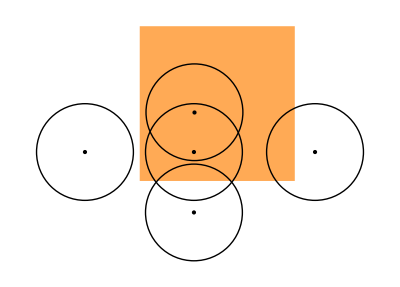

```mathematica
Graphics[{gABCD,g0,g1,g2,g3,g4}]
```

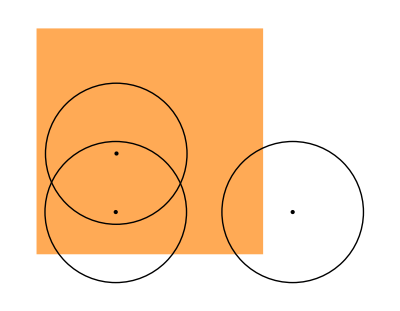

```mathematica
Graphics[{gABCD,g0,g1,g3}]
```

```mathematica
ans=NIntegrate[Boole[(x-pO[[1]])^2+(y-pO[[2]])^2>r^2&&(x-pO1[[1]])^2+(y-pO1[[2]])^2>r^2&&(x-pO3[[1]])^2+(y-pO3[[2]])^2>r^2],{x,0,d},{y,0,d},WorkingPrecision->20]
```

755.98683574685425438

```mathematica
Print[NumberForm[ans,6]];
```

755.987